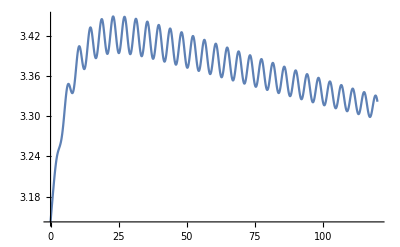

NDSolve::ndinnt: Initial condition a is not a number or a rectangular array of numbers.

ReplaceAll::rmix: Elements of {{x'[t]==y[t],y'[t]==-(0.01+0.225 Cos[«1»]) Sin[x[t]]-0.15 y[t]},x[0]==a,y[0]==b} are a mixture of lists and nonlists.

ReplaceAll::rmix: Elements of {{x'[10 π]==y[10 π],y'[10 π]==0.215 Sin[x[Times[«2»]]]-0.15 y[10 π]},x[0]==a,y[0]==b} are a mixture of lists and nonlists.

```mathematica
ClearSystemCache;
amp=0.10; ω=1.50; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=10*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

Export["w1.5.png",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]];

(*data=Flatten[Table[Table[{b,a,AttractingWell[a,b]},{a,0,2*Pi,0.05}],{b,0,2*Pi,0.05}],1];
Grid[data];
Export["w_0.5.dat",data];*)
```